```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY207/sec_int_data/675nm.dat"]
```

{{1.65577,0.110109},{1.59352,0.112971},{1.51672,0.120003},{1.46373,0.152292},{1.42047,0.159053},{1.37769,0.163818},{1.34607,0.176723},{1.31418,0.175884},{1.27734,0.169574},{1.24989,0.160161},{1.21939,0.191199},{1.20221,0.179735},{1.18519,0.140197},{1.17023,0.132168},{1.1572,0.0962189},{1.14604,0.0859942},{1.13497,0.0532564},{1.12762,-0.0628333},{1.12192,0.00299551},{1.11852,-0.0147584},{1.11638,0.00945516},{1.11532,0.0139029},{1.11466,0.151175},{1.11691,0.165091},{1.12052,0.210261},{1.12514,0.224343},{1.15252,0.190786},{1.18204,0.154179},{1.20774,0.243887},{1.24068,0.232935},{1.28541,0.23349},{1.36328,0.218171},{1.4246,0.222984}}

-0.0251587+0.130685 x

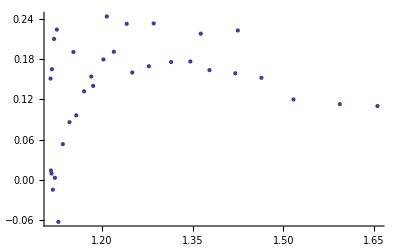

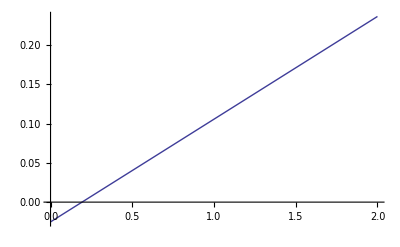

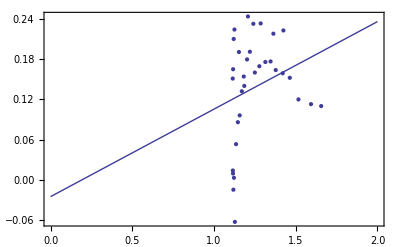

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```